```mathematica
data=Import["E:\\Excel\\data.csv"];data=data⟦2;;⟧;
```

```mathematica
amp=Interpolation[data⟦;;,{1,2}⟧]
```

InterpolatingFunction[…]

```mathematica
phase=Interpolation[data⟦;;,{1,3}⟧]
```

InterpolatingFunction[…]

```mathematica
fc=600;sol=FindRoot[{(20Log[10,Abs[(kp s+ki)/s]]+amp[f]//.{s->ⅈ 2π f,f->fc}//ComplexExpand)==0,ki/(2π kp)==fc/10},{{kp,1},{ki,1}}]
```

{kp→0.0261892,ki→9.87311}

```mathematica
fc=100;sol=FindRoot[{(20Log[10,Abs[(kp s+ki)/s]]+amp[f]//.{s->ⅈ 2π f,f->fc}//ComplexExpand)==0,ki/(2π kp)==fc/0.1},{{kp,1},{ki,1}}]
```

{kp→0.00195992,ki→12.3145}

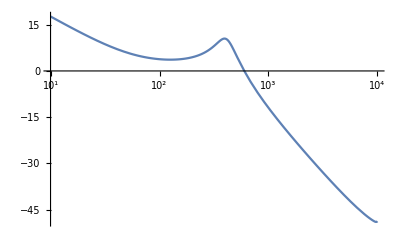

```mathematica
Plot[20Log[10,Abs[(kp s+ki)/s]]+amp[f]//.sol//.s->ⅈ 2π f//Evaluate,{f,10,10*^3},ScalingFunctions->{"Log10",None}](*fc=600Hz时环路增益幅频特性*)
```

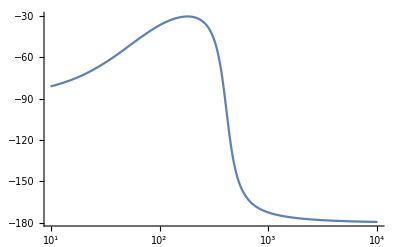

```mathematica
Plot[Arg[(kp s+ki)/s] 180/π+phase[f]//.sol//.s->ⅈ 2π f//Evaluate,{f,10,10*^3},ScalingFunctions->{"Log10",None}](*fc=600Hz时环路增益相频特性*)
```

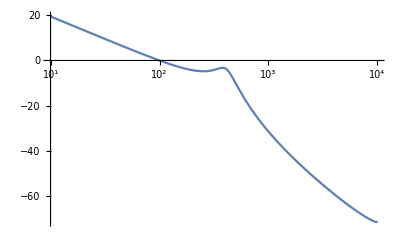

```mathematica
Plot[20Log[10,Abs[(kp s+ki)/s]]+amp[f]//.sol//.s->ⅈ 2π f//Evaluate,{f,10,10*^3},ScalingFunctions->{"Log10",None}](*fc=100Hz时环路增益幅频特性*)
```

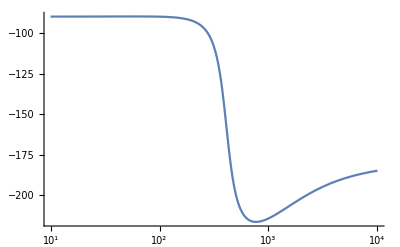

```mathematica
Plot[Arg[(kp s+ki)/s] 180/π+phase[f]//.sol//.s->ⅈ 2π f//Evaluate,{f,10,10*^3},ScalingFunctions->{"Log10",None}](*fc=100Hz时环路增益相频特性*)
```